[1/4] Generating Discrete AdS Spacetime (Steps: 1500)...

[2/4] Initializing Quantum Operators (Hamiltonian = Graph Laplacian)...

[3/4] Running Experiment A: Unobserved Quantum Evolution...

[4/4] Running Experiment B: The Observer Effect (Decoherence)...

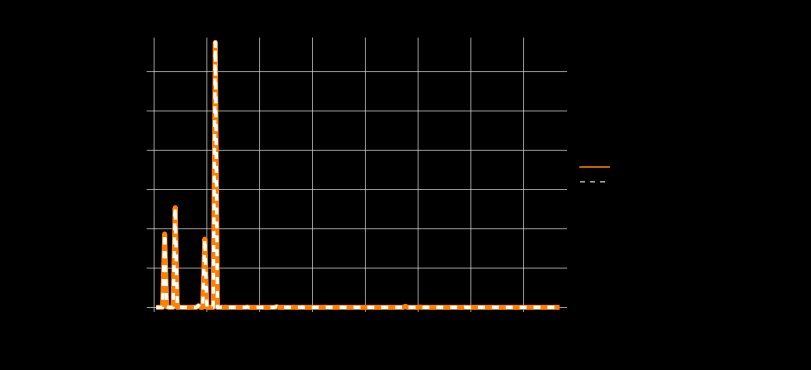

```mathematica
(* =========================================================================*)(*COMPUTATIONAL UNIVERSE:EMERGENT QUANTUM MECHANICS FROM GRAPH REWRITING*)(* =========================================================================*)(*Abstract:*)(*This experiment demonstrates how Quantum Interference and Wavefunction*)(*Collapse naturally emerge from a pre-geometric discrete graph model.*)(**)(*1. Background:An AdS-like discrete spacetime generated by the rule:*)(*{{x,y},{y,z}}->{{x,z},{x,w},{w,z}} with Causal Rigidity.*)(*2. Dynamics:Information propagation follows the discrete Schrodinger eq.*)(*d|Psi>/dt=-i*H* |Psi>,where H is the Graph Laplacian.*)(*3. Result:We observe the transition from Quantum Interference (M-shape)*)(*to Classical Distribution (Collapse) via simulated observation.*)(* =========================================================================*)(* ==========================================*)(*PART 1:The Spacetime Generator (The Bulk)*)(* ==========================================*)(*Core Rule:Causal Rigidity (Preserves history while expanding active boundary)*)rccRigidStep[g_Graph]:=Module[{allEdges,activeEdges,selectedPair,e1,e2,x,y,z,w,nextV,newActiveEdges,inertEdges},allEdges=EdgeList[g];
(*Only undirected edges are'active' (The Present)*)activeEdges=Cases[allEdges,_UndirectedEdge];
(*Monte Carlo Sampling for Performance*)Block[{shuffled=RandomSample[activeEdges]},Do[e1=shuffled[[i]];
Do[e2=shuffled[[j]];
(*Find causal pair {{x,y},{y,z}} sharing exactly one node*)If[Length[Intersection[List@@e1,List@@e2]]==1,selectedPair={e1,e2};
Goto["Found"];],{j,i+1,Min[i+20,Length[shuffled]]}],{i,1,Length[shuffled]}]];
Label["Found"];
If[Not[ValueQ[selectedPair]],Return[g]];
(*Rewrite Topology*){e1,e2}=selectedPair;
y=Intersection[List@@e1,List@@e2][[1]];
x=Complement[List@@e1,{y}][[1]];
z=Complement[List@@e2,{y}][[1]];
nextV=Max[VertexList[g]]+1;
w=nextV;
(*New active relations (The Quantum Boundary)*)newActiveEdges={x<->z,x<->w,w<->z};
(*Old relations become directed history (The Fixed Bulk)*)inertEdges={x->y,y->z};
(*Update Graph*)Graph[VertexList[g]~Join~{w},Union[Complement[allEdges,{e1,e2}],newActiveEdges,inertEdges]]];

(*Initialize Universe*)
initG=CycleGraph[4];
steps=1500; (*High resolution for interference patterns*)
Print["[1/4] Generating Discrete AdS Spacetime (Steps: ",steps,")..."];
universe=Nest[rccRigidStep,initG,steps];

(* ==========================================*)
(*PART 2:The Quantum Engine (Schrodinger)*)
(* ==========================================*)

Print["[2/4] Initializing Quantum Operators (Hamiltonian = Graph Laplacian)..."];

(*Graph Operators*)
adj=AdjacencyMatrix[universe];
deg=DiagonalMatrix[VertexDegree[universe]];
(*H=L=D-A (Kinetic Energy on Graph)*)
laplacian=N[deg-adj];

(*Define Double Slit Sources*)
(*We pick two nodes that are topologically close in the early universe*)
nodeList=VertexList[universe];
source1=nodeList[[2]];
source2=nodeList[[4]];
numNodes=VertexCount[universe];

(*Simulation Parameters*)
dt=0.05;          (*Time step*)
evolutionSteps=150; (*Duration*)
exposureTime=80;    (*For time-integrated measurement*)

(* ==========================================*)
(*PART 3:Experiment A-Unobserved (Interference)*)
(* ==========================================*)
Print["[3/4] Running Experiment A: Unobserved Quantum Evolution..."];

(*Initialize Wavefunction*)
psi=ConstantArray[0.0+0.0 I,numNodes];
psi[[source1]]=1.0;
psi[[source2]]=1.0;

accumulatedIntensity=ConstantArray[0.0,numNodes];

(*Evolution Loop*)
Do[(*Discrete Schrodinger Equation:Psi(t+1)=Psi(t)-i H Psi(t) dt*)psi=psi-I*dt*(laplacian.psi);
psi=psi/Norm[psi];(*Renormalization*)(*Accumulate Intensity for the last N steps (Long Exposure)*)If[t>(evolutionSteps-exposureTime),accumulatedIntensity+=Abs[psi]^2;];,{t,1,evolutionSteps}];

(* ==========================================*)
(*PART 4:Experiment B-Observed (Collapse)*)
(* ==========================================*)
Print["[4/4] Running Experiment B: The Observer Effect (Decoherence)..."];

(*Reset Wavefunction*)
psiObs=ConstantArray[0.0+0.0 I,numNodes];
psiObs[[source1]]=1.0;
psiObs[[source2]]=1.0;

accumulatedIntensityObs=ConstantArray[0.0,numNodes];

(*Evolution Loop with Observer*)
Do[psiObs=psiObs-I*dt*(laplacian.psiObs);
(*---THE MEASUREMENT ACT---*)(*Observer monitors Source 1,randomizing its phase relation with Source 2*)(*This simulates photon scattering/entropy injection*)psiObs[[source1]]=Abs[psiObs[[source1]]]*Exp[I*RandomReal[{0,2 Pi}]];
psiObs=psiObs/Norm[psiObs];
If[t>(evolutionSteps-exposureTime),accumulatedIntensityObs+=Abs[psiObs]^2;];,{t,1,evolutionSteps}];

(* ==========================================*)
(*PART 5:Data Extraction& Visualization*)
(* ==========================================*)

(*Define the'Screen'*)
(*We select nodes at a specific hop-distance to act as the detection screen*)
screenDistance=9;
screenNodes=Select[nodeList,GraphDistance[universe,source1,#]==screenDistance&];

(*Sort nodes by phase/topology to create a linear 1D screen view*)
(*Sorting by distance to source2 unfolds the angular distribution*)
sortedScreen=SortBy[screenNodes,GraphDistance[universe,source2,#]&];

(*Extract Data*)
dataInterference=accumulatedIntensity[[sortedScreen]];
dataCollapse=accumulatedIntensityObs[[sortedScreen]];

(*Plot The Grand Comparison*)
viz=ListLinePlot[{dataInterference,dataCollapse},PlotRange->All,PlotStyle->{{Thickness[0.006],Orange},(*Quantum*){Thickness[0.004],Dashed,White} (*Classical*)},PlotLegends->Placed[{Style["Unobserved (Quantum Interference)",12,Bold],Style["Observed (Wavefunction Collapse)",12]},{Right,Top}],Filling->{1->{2}},FillingStyle->Opacity[0.2,Red],PlotLabel->Style["Emergent Double-Slit Experiment\nin a Computational Universe",18,Bold,White],Frame->True,FrameLabel->{Style["Screen Position (Topological Order)",14,White],Style["Probability Density P(x)",14,White]},FrameStyle->Directive[White,Thickness[0.002]],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],Background->Black,ImageSize->600,BaseStyle->{FontFamily->"Helvetica",FontSize->12}];

(*Output*)
viz
```